# YM

```mathematica
NotebookDirectory[]
```

/home/raj/C_SM/ToySMat1Loop/

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$model="YM";
```

```mathematica
<<GenAmp`
```

Patched 2 FeynArts models.

## Setup

```mathematica
$gaugerules={FAGaugeXi[_V]:> FAGaugeXi[V[1]]};
```

```mathematica
$ampconfigFCFAConvert={ChangeDimension->D,Contract->False,DropSumOver->True,FCFADiracChainJoin->True,FeynAmpDenominatorCombine->True,
FinalSubstitutions->{},InitialSubstitutions->{},List->False,LoopMomenta->{l},LorentzIndexNames->{},Prefactor->1,SMP->True,SUNFIndexNames->{},
SUNIndexNames->{},TransversePolarizationVectors->{},UndoChiralSplittings->True};
```

```mathematica
fSimp[exp_]:=exp//SUNSimplify[#,SUNNToCACF->False,Explicit->True]&;
```

## Tadpoles (1->0)

## One Loop A->0

loading generic model file /home/raj/C_SM/ToySMat1Loop/models/YM/YM.gen

> $GenericMixing is OFF

generic model {./models/YM/YM} initialized

loading classes model file /home/raj/C_SM/ToySMat1Loop/models/YM/YM.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

> 5 counterterms of order 1

classes model {./models/YM/YM} initialized

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 ab/0/bb.m, 0 diagrams

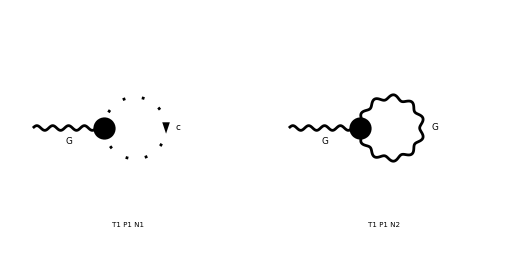

```mathematica
D1LA=diag[1,{V[1]},{}];
```

```mathematica
Amp1LA=D1LA//amp1L[{p1},{}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

Part::partw: Part 2 of {} does not exist.

{0,0}

## One Loop (1->1)

## One Loop A->A

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 2 Particles insertions

in total: 3 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

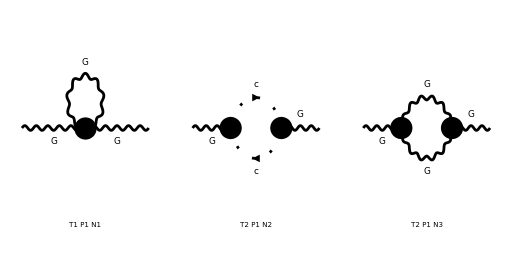

> Top. 1 ac/bc/0.m, 0 diagrams

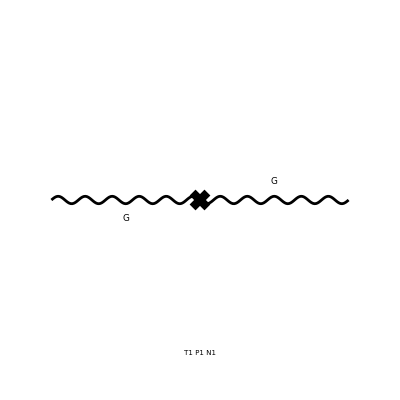

```mathematica
D1LAA=diag[1,{V[1]},{V[1]}];
```

```mathematica
Amp1LAA=D1LAA//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 2 Particles amplitudes

in total: 3 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ (g l^Lor1 f^Glu1Glu3Glu4-g p1^Lor1 f^Glu1Glu3Glu4) (g (p1-l)^Lor2 f^Glu2Glu3Glu4-g p1^Lor2 f^Glu2Glu3Glu4))/(16 π^4 l^2.(l-p1)^2)+1/(32 π^4)ⅈ (-((1-ξ_(V(1)))^2 l^Lor3 l^Lor4 (l-p1)^Lor5 (p1-l)^Lor6)/((l^2)^2.((l-p1)^2)^2)-((1-ξ_(V(1))) l^Lor3 l^Lor4 g^Lor5Lor6)/((l^2)^2.(l-p1)^2)+((1-ξ_(V(1))) g^Lor3Lor4 (l-p1)^Lor5 (p1-l)^Lor6)/(l^2.((l-p1)^2)^2)+(g^Lor3Lor4 g^Lor5Lor6)/(l^2.(l-p1)^2)) (-g l^Lor1 g^Lor3Lor5 f^Glu1Glu3Glu4+g (p1-l)^Lor1 g^Lor3Lor5 f^Glu1Glu3Glu4+g g^Lor1Lor5 (l-p1)^Lor3 f^Glu1Glu3Glu4-g g^Lor1Lor5 p1^Lor3 f^Glu1Glu3Glu4+g g^Lor1Lor3 l^Lor5 f^Glu1Glu3Glu4+g g^Lor1Lor3 p1^Lor5 f^Glu1Glu3Glu4) (g l^Lor2 g^Lor4Lor6 f^Glu2Glu3Glu4+g (l-p1)^Lor2 g^Lor4Lor6 f^Glu2Glu3Glu4+g g^Lor2Lor6 p1^Lor4 f^Glu2Glu3Glu4+g g^Lor2Lor6 (p1-l)^Lor4 f^Glu2Glu3Glu4-g g^Lor2Lor4 l^Lor6 f^Glu2Glu3Glu4-g g^Lor2Lor4 p1^Lor6 f^Glu2Glu3Glu4)-((g^Lor3Lor4/l^2-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2)^2)) (ⅈ g^Lor1Lor3 g^Lor2Lor4 f^Glu1Glu3$AL$10911 f^Glu2Glu3$AL$10911 g^2-2 ⅈ g^Lor1Lor2 g^Lor3Lor4 f^Glu1Glu3$AL$10912 f^Glu2Glu3$AL$10912 g^2+ⅈ g^Lor1Lor4 g^Lor2Lor3 f^Glu1Glu3$AL$10914 f^Glu2Glu3$AL$10914 g^2))/(32 π^4),-ⅈ (ⅈ (ZG-1) p1^Lor1 p1^Lor2 δ^Glu1Glu2-ⅈ (ZG-1) g^Lor1Lor2 p1^2 δ^Glu1Glu2)}

```mathematica
Amp1LAADiv=Amp1LAA//amp1LSimplify[{ZG:> 1+Nd dG},{SMP["Delta"],dG}]//fSimp
```

-dG p1^2 g^Lor1Lor2 δ^Glu1Glu2+dG p1^Lor1 p1^Lor2 δ^Glu1Glu2-(13 Δ g^2 N p1^Lor1 p1^Lor2 δ^Glu1Glu2)/(48 π^2)+(13 Δ g^2 N p1^2 g^Lor1Lor2 δ^Glu1Glu2)/(48 π^2)+(Δ g^2 N p1^Lor1 p1^Lor2 ξ_(V(1)) δ^Glu1Glu2)/(16 π^2)-(Δ g^2 N p1^2 ξ_(V(1)) g^Lor1Lor2 δ^Glu1Glu2)/(16 π^2)

```mathematica
dsol[1]=Solve[SelectNotFree2[Amp1LAADiv,{SMP["Delta"],dG}]==0,dG]//Flatten//Simplify
dSave[dsol[1]];
```

{dG→(Δ g^2 N (13-3 ξ_(V(1))))/(48 π^2)}

## One Loop c->c

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bd/cdcd.m, 0 diagrams

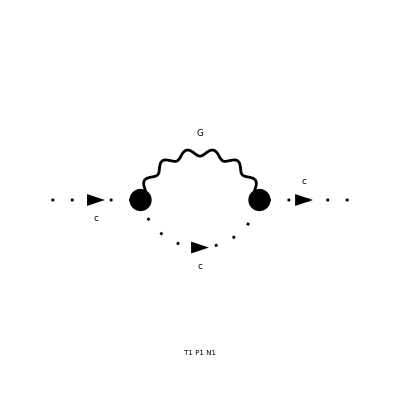

> Top. 1 ac/bc/0.m, 0 diagrams

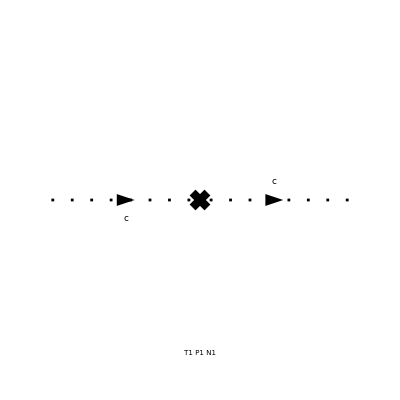

```mathematica
D1Lcc=diag[1,{U[1]},{U[1]}];
```

```mathematica
Amp1Lcc=D1Lcc//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ (-g (l-p1)^Lor1 f^Glu1Glu3Glu4-g p1^Lor1 f^Glu1Glu3Glu4) (g (p1-l)^Lor2 f^Glu2Glu3Glu4+g l^Lor2 f^Glu2Glu3Glu4) (g^Lor1Lor2/(l^2.(l-p1)^2)+((1-ξ_(V(1))) (l-p1)^Lor1 (p1-l)^Lor2)/(l^2.((l-p1)^2)^2)))/(16 π^4),p1^2 (Zc-1) δ^Glu1Glu2}

```mathematica
Amp1LccDiv=Amp1Lcc//amp1LSimplify[{Zc:> 1+Nd dc},{SMP["Delta"],dc}]//fSimp
```

dc p1^2 δ^Glu1Glu2-(3 Δ g^2 N p1^2 δ^Glu1Glu2)/(32 π^2)+(Δ g^2 N p1^2 ξ_(V(1)) δ^Glu1Glu2)/(32 π^2)

```mathematica
dsol[2]=Solve[SelectNotFree2[Amp1LccDiv,{SMP["Delta"],dc}]==0,dc]//Flatten//Simplify
dSave[dsol[2]];
```

{dc→-(Δ g^2 N (ξ_(V(1))-3))/(32 π^2)}

## One Loop (2->1)

## One Loop AA->A

inserting at level(s) {Particles}

> Top. 1: 3 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 6 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 adbe/cf/dedfef.m, 0 diagrams

> Top. 2 adbe/ce/dede.m, 0 diagrams

> Top. 3 adbe/cd/eded.m, 0 diagrams

> Top. 4 adbd/ce/eded.m, 0 diagrams

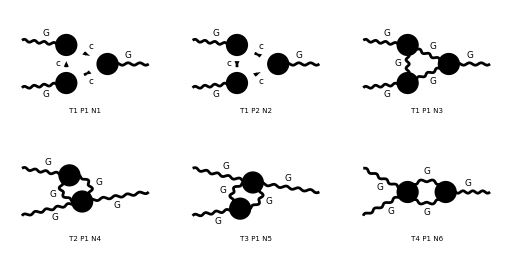

> Top. 1 adbd/cd/0.m, 0 diagrams

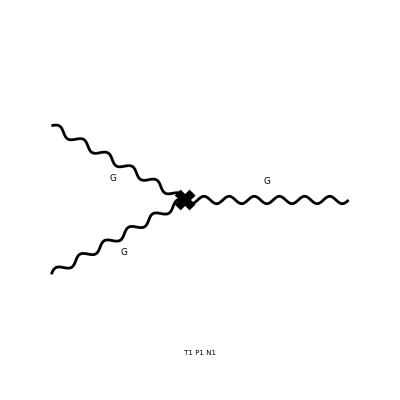

```mathematica
D1LAAA=diag[1,{V[1],V[1]},{V[1]}];
```

```mathematica
Amp1LAAA=D1LAAA//amp1L[{p1,p1},{2p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 6 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{((g l^Lor1 f^Glu1Glu4Glu5-g p1^Lor1 f^Glu1Glu4Glu5) (g (-l-p1)^Lor2 f^Glu2Glu4Glu6+g p1^Lor2 f^Glu2Glu4Glu6) (2 g p1^Lor3 f^Glu3Glu5Glu6-g (p1-l)^Lor3 f^Glu3Glu5Glu6))/(16 π^4 l^2.(l+p1)^2.(l-p1)^2)+((g (l-p1)^Lor1 f^Glu1Glu4Glu5+g p1^Lor1 f^Glu1Glu4Glu5) (-g l^Lor2 f^Glu2Glu4Glu6-g p1^Lor2 f^Glu2Glu4Glu6) (g (l+p1)^Lor3 f^Glu3Glu5Glu6-2 g p1^Lor3 f^Glu3Glu5Glu6))/(16 π^4 l^2.(l+p1)^2.(l-p1)^2)+1/(16 π^4)(-((1-ξ_(V(1)))^3 l^Lor4 l^Lor5 (l-p1)^Lor6 (p1-l)^Lor7 (-l-p1)^Lor8 (l+p1)^Lor9)/((l^2)^2.((l+p1)^2)^2.((l-p1)^2)^2)-((1-ξ_(V(1)))^2 l^Lor4 l^Lor5 (l-p1)^Lor6 (p1-l)^Lor7 g^Lor8Lor9)/((l^2)^2.(l+p1)^2.((l-p1)^2)^2)-((1-ξ_(V(1)))^2 l^Lor4 l^Lor5 g^Lor6Lor7 (-l-p1)^Lor8 (l+p1)^Lor9)/((l^2)^2.((l+p1)^2)^2.(l-p1)^2)+((1-ξ_(V(1)))^2 g^Lor4Lor5 (l-p1)^Lor6 (p1-l)^Lor7 (-l-p1)^Lor8 (l+p1)^Lor9)/(l^2.((l+p1)^2)^2.((l-p1)^2)^2)-((1-ξ_(V(1))) l^Lor4 l^Lor5 g^Lor6Lor7 g^Lor8Lor9)/((l^2)^2.(l+p1)^2.(l-p1)^2)+((1-ξ_(V(1))) g^Lor4Lor5 (l-p1)^Lor6 (p1-l)^Lor7 g^Lor8Lor9)/(l^2.(l+p1)^2.((l-p1)^2)^2)+((1-ξ_(V(1))) g^Lor4Lor5 g^Lor6Lor7 (-l-p1)^Lor8 (l+p1)^Lor9)/(l^2.((l+p1)^2)^2.(l-p1)^2)+(g^Lor4Lor5 g^Lor6Lor7 g^Lor8Lor9)/(l^2.(l+p1)^2.(l-p1)^2)) (-g l^Lor1 g^Lor4Lor6 f^Glu1Glu4Glu5+g (p1-l)^Lor1 g^Lor4Lor6 f^Glu1Glu4Glu5+g g^Lor1Lor6 (l-p1)^Lor4 f^Glu1Glu4Glu5-g g^Lor1Lor6 p1^Lor4 f^Glu1Glu4Glu5+g g^Lor1Lor4 l^Lor6 f^Glu1Glu4Glu5+g g^Lor1Lor4 p1^Lor6 f^Glu1Glu4Glu5) (g l^Lor2 g^Lor5Lor8 f^Glu2Glu4Glu6+g (l+p1)^Lor2 g^Lor5Lor8 f^Glu2Glu4Glu6+g g^Lor2Lor8 (-l-p1)^Lor5 f^Glu2Glu4Glu6-g g^Lor2Lor8 p1^Lor5 f^Glu2Glu4Glu6-g g^Lor2Lor5 l^Lor8 f^Glu2Glu4Glu6+g g^Lor2Lor5 p1^Lor8 f^Glu2Glu4Glu6) (g (-l-p1)^Lor3 g^Lor7Lor9 f^Glu3Glu5Glu6+g (p1-l)^Lor3 g^Lor7Lor9 f^Glu3Glu5Glu6+2 g g^Lor3Lor9 p1^Lor7 f^Glu3Glu5Glu6+g g^Lor3Lor9 (l+p1)^Lor7 f^Glu3Glu5Glu6+g g^Lor3Lor7 (l-p1)^Lor9 f^Glu3Glu5Glu6-2 g g^Lor3Lor7 p1^Lor9 f^Glu3Glu5Glu6)+1/(32 π^4)ⅈ (-((1-ξ_(V(1)))^2 l^Lor4 l^Lor5 (l-p1)^Lor6 (p1-l)^Lor7)/((l^2)^2.((l-p1)^2)^2)-((1-ξ_(V(1))) l^Lor4 l^Lor5 g^Lor6Lor7)/((l^2)^2.(l-p1)^2)+((1-ξ_(V(1))) g^Lor4Lor5 (l-p1)^Lor6 (p1-l)^Lor7)/(l^2.((l-p1)^2)^2)+(g^Lor4Lor5 g^Lor6Lor7)/(l^2.(l-p1)^2)) (-g l^Lor1 g^Lor4Lor6 f^Glu1Glu4Glu5+g (p1-l)^Lor1 g^Lor4Lor6 f^Glu1Glu4Glu5+g g^Lor1Lor6 (l-p1)^Lor4 f^Glu1Glu4Glu5-g g^Lor1Lor6 p1^Lor4 f^Glu1Glu4Glu5+g g^Lor1Lor4 l^Lor6 f^Glu1Glu4Glu5+g g^Lor1Lor4 p1^Lor6 f^Glu1Glu4Glu5) (-ⅈ g^Lor2Lor3 g^Lor5Lor7 (f^Glu2Glu5$AL$13805 f^Glu3Glu4$AL$13805+f^Glu2Glu4$AL$13804 f^Glu3Glu5$AL$13804) g^2+ⅈ g^Lor2Lor7 g^Lor3Lor5 (f^Glu2Glu4$AL$13801 f^Glu3Glu5$AL$13801+f^Glu2Glu3$AL$13800 f^Glu4Glu5$AL$13800) g^2-ⅈ g^Lor2Lor5 g^Lor3Lor7 (f^Glu2Glu3$AL$13802 f^Glu4Glu5$AL$13802-f^Glu2Glu5$AL$13803 f^Glu3Glu4$AL$13803) g^2)+1/(32 π^4)ⅈ (-((1-ξ_(V(1)))^2 l^Lor4 l^Lor5 (l-p1)^Lor6 (p1-l)^Lor7)/((l^2)^2.((l-p1)^2)^2)-((1-ξ_(V(1))) l^Lor4 l^Lor5 g^Lor6Lor7)/((l^2)^2.(l-p1)^2)+((1-ξ_(V(1))) g^Lor4Lor5 (l-p1)^Lor6 (p1-l)^Lor7)/(l^2.((l-p1)^2)^2)+(g^Lor4Lor5 g^Lor6Lor7)/(l^2.(l-p1)^2)) (-g l^Lor2 g^Lor4Lor6 f^Glu2Glu4Glu5+g (p1-l)^Lor2 g^Lor4Lor6 f^Glu2Glu4Glu5+g g^Lor2Lor6 (l-p1)^Lor4 f^Glu2Glu4Glu5-g g^Lor2Lor6 p1^Lor4 f^Glu2Glu4Glu5+g g^Lor2Lor4 l^Lor6 f^Glu2Glu4Glu5+g g^Lor2Lor4 p1^Lor6 f^Glu2Glu4Glu5) (-ⅈ g^Lor1Lor3 g^Lor5Lor7 (f^Glu1Glu5$AL$13811 f^Glu3Glu4$AL$13811+f^Glu1Glu4$AL$13810 f^Glu3Glu5$AL$13810) g^2+ⅈ g^Lor1Lor7 g^Lor3Lor5 (f^Glu1Glu4$AL$13807 f^Glu3Glu5$AL$13807+f^Glu1Glu3$AL$13806 f^Glu4Glu5$AL$13806) g^2-ⅈ g^Lor1Lor5 g^Lor3Lor7 (f^Glu1Glu3$AL$13808 f^Glu4Glu5$AL$13808-f^Glu1Glu5$AL$13809 f^Glu3Glu4$AL$13809) g^2)+1/(32 π^4)ⅈ (-((1-ξ_(V(1)))^2 l^Lor4 l^Lor5 (l+2 p1)^Lor6 (-l-2 p1)^Lor7)/((l^2)^2.((l+2 p1)^2)^2)-((1-ξ_(V(1))) l^Lor4 l^Lor5 g^Lor6Lor7)/((l^2)^2.(l+2 p1)^2)+((1-ξ_(V(1))) g^Lor4Lor5 (l+2 p1)^Lor6 (-l-2 p1)^Lor7)/(l^2.((l+2 p1)^2)^2)+(g^Lor4Lor5 g^Lor6Lor7)/(l^2.(l+2 p1)^2)) (-g l^Lor3 g^Lor4Lor6 f^Glu3Glu4Glu5+g (-l-2 p1)^Lor3 g^Lor4Lor6 f^Glu3Glu4Glu5+2 g g^Lor3Lor6 p1^Lor4 f^Glu3Glu4Glu5+g g^Lor3Lor6 (l+2 p1)^Lor4 f^Glu3Glu4Glu5+g g^Lor3Lor4 l^Lor6 f^Glu3Glu4Glu5-2 g g^Lor3Lor4 p1^Lor6 f^Glu3Glu4Glu5) (-ⅈ g^Lor1Lor2 g^Lor5Lor7 (f^Glu1Glu5$AL$13817 f^Glu2Glu4$AL$13817+f^Glu1Glu4$AL$13816 f^Glu2Glu5$AL$13816) g^2+ⅈ g^Lor1Lor7 g^Lor2Lor5 (f^Glu1Glu4$AL$13813 f^Glu2Glu5$AL$13813+f^Glu1Glu2$AL$13812 f^Glu4Glu5$AL$13812) g^2-ⅈ g^Lor1Lor5 g^Lor2Lor7 (f^Glu1Glu2$AL$13814 f^Glu4Glu5$AL$13814-f^Glu1Glu5$AL$13815 f^Glu2Glu4$AL$13815) g^2),-ⅈ (3 g (ZG^(3/2) ZG3-1) p1^Lor1 g^Lor2Lor3 f^Glu1Glu2Glu3-3 g (ZG^(3/2) ZG3-1) g^Lor1Lor3 p1^Lor2 f^Glu1Glu2Glu3)}

```mathematica
Amp1LAAADiv=Amp1LAAA//amp1LSimplify[{ZG:> 1+Nd dG,ZG3:>1+Nd dG3},{SMP["Delta"],dG,dG3}]//fSimp
```

-9 dG g p1^Lor1 g^Lor2Lor3 (tr(T^Glu1.T^Glu2.T^Glu3))+9 dG g p1^Lor2 g^Lor1Lor3 (tr(T^Glu1.T^Glu2.T^Glu3))+9 dG g p1^Lor1 g^Lor2Lor3 (tr(T^Glu2.T^Glu1.T^Glu3))-9 dG g p1^Lor2 g^Lor1Lor3 (tr(T^Glu2.T^Glu1.T^Glu3))-6 dG3 g p1^Lor1 g^Lor2Lor3 (tr(T^Glu1.T^Glu2.T^Glu3))+6 dG3 g p1^Lor2 g^Lor1Lor3 (tr(T^Glu1.T^Glu2.T^Glu3))+6 dG3 g p1^Lor1 g^Lor2Lor3 (tr(T^Glu2.T^Glu1.T^Glu3))-6 dG3 g p1^Lor2 g^Lor1Lor3 (tr(T^Glu2.T^Glu1.T^Glu3))+(17 Δ g^3 N p1^Lor1 g^Lor2Lor3 (tr(T^Glu1.T^Glu2.T^Glu3)))/(16 π^2)-(17 Δ g^3 N p1^Lor2 g^Lor1Lor3 (tr(T^Glu1.T^Glu2.T^Glu3)))/(16 π^2)-(17 Δ g^3 N p1^Lor1 g^Lor2Lor3 (tr(T^Glu2.T^Glu1.T^Glu3)))/(16 π^2)+(17 Δ g^3 N p1^Lor2 g^Lor1Lor3 (tr(T^Glu2.T^Glu1.T^Glu3)))/(16 π^2)-(9 Δ g^3 N p1^Lor1 ξ_(V(1)) g^Lor2Lor3 (tr(T^Glu1.T^Glu2.T^Glu3)))/(16 π^2)+(9 Δ g^3 N p1^Lor2 ξ_(V(1)) g^Lor1Lor3 (tr(T^Glu1.T^Glu2.T^Glu3)))/(16 π^2)+(9 Δ g^3 N p1^Lor1 ξ_(V(1)) g^Lor2Lor3 (tr(T^Glu2.T^Glu1.T^Glu3)))/(16 π^2)-(9 Δ g^3 N p1^Lor2 ξ_(V(1)) g^Lor1Lor3 (tr(T^Glu2.T^Glu1.T^Glu3)))/(16 π^2)

```mathematica
dsol[3]=Solve[SelectNotFree2[Amp1LAAADiv/.dSub[dG3],{SMP["Delta"],dG3}]==0,dG3]//Flatten//Simplify
dSave[dsol[3]];
```

{dG3→-(11 Δ g^2 N)/(48 π^2)}

## One Loop cc->A

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 adbe/cf/dedfef.m, 0 diagrams

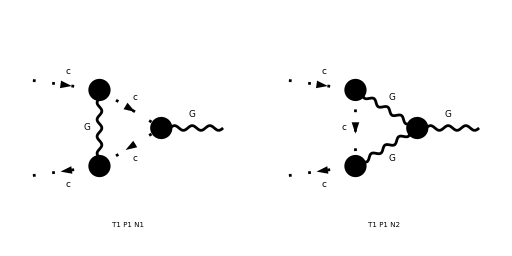

> Top. 1 adbd/cd/0.m, 0 diagrams

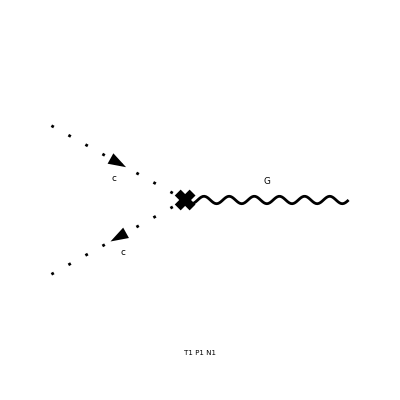

```mathematica
D1LccA=diag[1,{U[1],-U[1]},{V[1]}];
```

```mathematica
Amp1LccA=D1LccA//amp1L[{p1,p1},{2p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{((g p1^Lor2 f^Glu1Glu4Glu5-g l^Lor2 f^Glu1Glu4Glu5) (-g (-l-p1)^Lor3 f^Glu2Glu4Glu6-g l^Lor3 f^Glu2Glu4Glu6) (2 g p1^Lor1 f^Glu3Glu5Glu6-g (p1-l)^Lor1 f^Glu3Glu5Glu6) (g^Lor2Lor3/(l^2.(l+p1)^2.(l-p1)^2)-(l^Lor2 l^Lor3 (1-ξ_(V(1))))/((l^2)^2.(l+p1)^2.(l-p1)^2)))/(16 π^4)-1/(16 π^4)(-g (l-p1)^Lor2 f^Glu1Glu4Glu5-g p1^Lor2 f^Glu1Glu4Glu5) (g (-l-p1)^Lor4 f^Glu2Glu4Glu6+g l^Lor4 f^Glu2Glu4Glu6) (g g^Lor3Lor5 (-l-p1)^Lor1 f^Glu3Glu5Glu6+g g^Lor3Lor5 (p1-l)^Lor1 f^Glu3Glu5Glu6+g g^Lor1Lor5 (l+p1)^Lor3 f^Glu3Glu5Glu6+g g^Lor1Lor3 (l-p1)^Lor5 f^Glu3Glu5Glu6+2 g p1^Lor3 g^Lor1Lor5 f^Glu3Glu5Glu6-2 g p1^Lor5 g^Lor1Lor3 f^Glu3Glu5Glu6) (((1-ξ_(V(1))) g^Lor4Lor5 (l-p1)^Lor2 (p1-l)^Lor3)/(l^2.(l+p1)^2.((l-p1)^2)^2)+((1-ξ_(V(1))) g^Lor2Lor3 (-l-p1)^Lor4 (l+p1)^Lor5)/(l^2.((l+p1)^2)^2.(l-p1)^2)+(g^Lor2Lor3 g^Lor4Lor5)/(l^2.(l+p1)^2.(l-p1)^2)+((1-ξ_(V(1)))^2 (l-p1)^Lor2 (p1-l)^Lor3 (-l-p1)^Lor4 (l+p1)^Lor5)/(l^2.((l+p1)^2)^2.((l-p1)^2)^2)),-ⅈ g p1^Lor1 (Zc √ZG ZGcc-1) f^Glu1Glu2Glu3}

```mathematica
Amp1LccADiv=Amp1LccA//amp1LSimplify[{ZG:> 1+Nd dG,ZGcc:> 1+Nd dGcc,Zc->1+Nd dc},{SMP["Delta"],dG,dGcc,dc}]//fSimp
```

-2 dc g p1^Lor1 (tr(T^Glu1.T^Glu2.T^Glu3))+2 dc g p1^Lor1 (tr(T^Glu2.T^Glu1.T^Glu3))-dG g p1^Lor1 (tr(T^Glu1.T^Glu2.T^Glu3))+dG g p1^Lor1 (tr(T^Glu2.T^Glu1.T^Glu3))-2 dGcc g p1^Lor1 (tr(T^Glu1.T^Glu2.T^Glu3))+2 dGcc g p1^Lor1 (tr(T^Glu2.T^Glu1.T^Glu3))-(Δ g^3 N p1^Lor1 ξ_(V(1)) (tr(T^Glu1.T^Glu2.T^Glu3)))/(8 π^2)+(Δ g^3 N p1^Lor1 ξ_(V(1)) (tr(T^Glu2.T^Glu1.T^Glu3)))/(8 π^2)

```mathematica
dsol[4]=Solve[SelectNotFree2[Amp1LccADiv/.dSub[dGcc],{SMP["Delta"],dGcc}]==0,dGcc]//Flatten//Simplify
dSave[dsol[4]];
```

{dGcc→-(11 Δ g^2 N)/(48 π^2)}

## One Loop (2->2)

## One Loop VV->VV

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

> Top. 5: 1 Particles insertion

> Top. 6: 1 Particles insertion

> Top. 7: 3 Particles insertions

> Top. 8: 3 Particles insertions

> Top. 9: 3 Particles insertions

> Top. 10: 1 Particles insertion

> Top. 11: 1 Particles insertion

> Top. 12: 1 Particles insertion

in total: 18 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

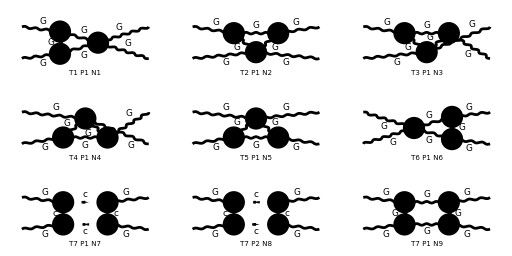

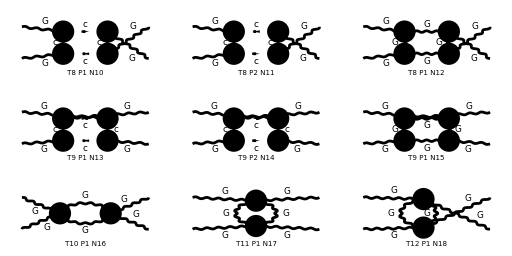

> Top. 1 aebe/cede/0.m, 0 diagrams

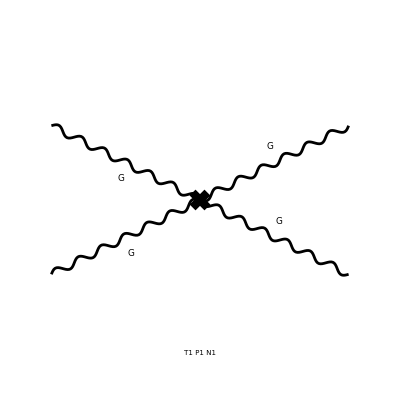

```mathematica
D1LAAAA=diag[1,{V[1],V[1]},{V[1],V[1]}];
```

```mathematica
Amp1LAAAA=D1LAAAA//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

> Top. 5: 1 Particles amplitude

> Top. 6: 1 Particles amplitude

> Top. 7: 3 Particles amplitudes

> Top. 8: 3 Particles amplitudes

> Top. 9: 3 Particles amplitudes

> Top. 10: 1 Particles amplitude

> Top. 11: 1 Particles amplitude

> Top. 12: 1 Particles amplitude

in total: 18 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ (g (l-p1)^Lor1 f^Glu1Glu5Glu6+g p1^Lor1 f^Glu1Glu5Glu6) (-g (l-p1)^Lor2 f^Glu2Glu7Glu8-g p1^Lor2 f^Glu2Glu7Glu8) (g p1^Lor3 f^Glu3Glu5Glu7-g l^Lor3 f^Glu3Glu5Glu7) (g l^Lor4 f^Glu4Glu6Glu8-g p1^Lor4 f^Glu4Glu6Glu8))/(16 π^4 l^2.(l-p1)^2.l^2.(l-p1)^2)+(ⅈ 3 (g l^Lor4 f^Glu4Glu6Glu8-g p1^Lor4 f^Glu4Glu6Glu8))/(16 π^4 l^2.(l+p1)^2.l^2.(l-p1)^2)+(ⅈ 3 (1-1))/(16 π^4 1)+15+1/(16 1)+((10+1/1) (1) 1 (1))/(16 π^4)+((10+(g^11 111)/(l^2.1^2.1^2)) 2 (-ⅈ g^Lor1Lor2 g^Lor10Lor8 (f^Glu1Glu7$AL$19181 f^Glu2Glu6$AL$19181+f^Glu1Glu61 f^1) g^2+ⅈ 3 g^2-ⅈ 3 g^2))/(16 π^4),1}
 |  |  |  |

```mathematica
Amp1LAAAADiv=Amp1LAAAA//amp1LSimplify[{ZG:> 1+Nd dG,ZG4:> 1+Nd dG4},{SMP["Delta"],dG,dG4},True]//fSimp
```

Current diagram:       Number of diagrams: 18

Time: 1060.72 s

(N g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^4)/(4 π^2)-(N g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^4)/(3 π^2)+(N ξ_(V(1)) g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^4)/(2 π^2)+(N g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^4)/(4 π^2)+(N g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^4)/(4 π^2)+(N g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^4)/(4 π^2)-(N g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^4)/(3 π^2)+(N ξ_(V(1)) g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^4)/(2 π^2)-(N g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^4)/(3 π^2)+(N ξ_(V(1)) g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^4)/(2 π^2)+(N g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^4)/(4 π^2)+(N g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^4)/(4 π^2)+(N g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^4)/(4 π^2)+(N g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^4)/(4 π^2)-(N g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^4)/(3 π^2)+(N ξ_(V(1)) g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^4)/(2 π^2)-(N g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^4)/(3 π^2)+(N ξ_(V(1)) g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^4)/(2 π^2)+(N g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^4)/(4 π^2)+(N g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^4)/(4 π^2)+(N g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor4 g^Lor2Lor3 Δ (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^4)/(4 π^2)-(N g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^4)/(3 π^2)+(N ξ_(V(1)) g^Lor1Lor3 g^Lor2Lor4 Δ (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^4)/(2 π^2)+(N g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^4)/(6 π^2)-(N ξ_(V(1)) g^Lor1Lor2 g^Lor3Lor4 Δ (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^4)/(4 π^2)-4 dG g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^2-2 dG4 g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^2+8 dG g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^2+4 dG4 g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^2-4 dG g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^2-2 dG4 g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu1.T^Glu2.T^Glu3.T^Glu4)) g^2-4 dG g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^2-2 dG4 g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^2-4 dG g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^2-2 dG4 g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^2+8 dG g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^2+4 dG4 g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu1.T^Glu3.T^Glu2.T^Glu4)) g^2+8 dG g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^2+4 dG4 g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^2-4 dG g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^2-2 dG4 g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^2-4 dG g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^2-2 dG4 g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu2.T^Glu1.T^Glu3.T^Glu4)) g^2-4 dG g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^2-2 dG4 g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^2-4 dG g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^2-2 dG4 g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^2+8 dG g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^2+4 dG4 g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu2.T^Glu3.T^Glu1.T^Glu4)) g^2+8 dG g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^2+4 dG4 g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^2-4 dG g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^2-2 dG4 g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^2-4 dG g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^2-2 dG4 g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu3.T^Glu1.T^Glu2.T^Glu4)) g^2-4 dG g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^2-2 dG4 g^Lor1Lor4 g^Lor2Lor3 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^2+8 dG g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^2+4 dG4 g^Lor1Lor3 g^Lor2Lor4 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^2-4 dG g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^2-2 dG4 g^Lor1Lor2 g^Lor3Lor4 (tr(T^Glu3.T^Glu2.T^Glu1.T^Glu4)) g^2

```mathematica
dsol[5]=Solve[SelectNotFree2[Amp1LAAAADiv/.dSub[dG4],{SMP["Delta"],dG4}]==0,dG4]//Flatten//Simplify
dSave[dsol[5]];
```

{dG4→-(11 Δ g^2 N)/(24 π^2)}

## One Loop UU->VV

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 2 Particles insertions

> Top. 9: 2 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

in total: 7 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 3 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 4 aebf/cgdh/egehfgfh.m, 0 diagrams

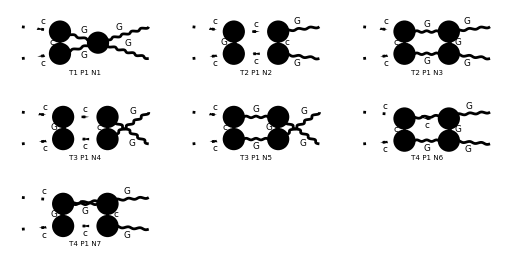

```mathematica
D1LUUAA=diag[1,{U[1],-U[1]},{V[1],V[1]}];
```

```mathematica
Amp1LUUAA=D1LUUAA//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 7 Particles amplitudes

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

{-1/(16 π^4)ⅈ (-((1-ξ_(V(1)))^2 l^Lor3 l^Lor4 (l-p1)^Lor5 (p1-l)^Lor6)/((l^2)^2.((l-p1)^2)^2.l^2.(l-p1)^2)-((1-ξ_(V(1))) l^Lor3 l^Lor4 g^Lor5Lor6)/((l^2)^2.(l-p1)^2.l^2.(l-p1)^2)+((1-ξ_(V(1))) g^Lor3Lor4 (l-p1)^Lor5 (p1-l)^Lor6)/(l^2.((l-p1)^2)^2.l^2.(l-p1)^2)+(g^Lor3Lor4 g^Lor5Lor6)/(l^2.(l-p1)^2.l^2.(l-p1)^2)) (g p1^Lor3 f^Glu1Glu5Glu6-g l^Lor3 f^Glu1Glu5Glu6) (g l^Lor5 f^Glu2Glu7Glu8-g (l-p1)^Lor5 f^Glu2Glu7Glu8) (g l^Lor1 g^Lor4Lor6 f^Glu3Glu5Glu7+g (l-p1)^Lor1 g^Lor4Lor6 f^Glu3Glu5Glu7+g g^Lor1Lor6 p1^Lor4 f^Glu3Glu5Glu7+g g^Lor1Lor6 (p1-l)^Lor4 f^Glu3Glu5Glu7-g g^Lor1Lor4 l^Lor6 f^Glu3Glu5Glu7-g g^Lor1Lor4 p1^Lor6 f^Glu3Glu5Glu7) (g p1^Lor2 f^Glu4Glu6Glu8-g (p1-l)^Lor2 f^Glu4Glu6Glu8)+1/(16 π^4)ⅈ (g^Lor3Lor4/(l^2.(l+p1)^2.l^2.(l-p1)^2)-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2)^2.(l+p1)^2.l^2.(l-p1)^2)) (g p1^Lor3 f^Glu1Glu5Glu6-g l^Lor3 f^Glu1Glu5Glu6) (-g l^Lor4 f^Glu2Glu5Glu7-g (-l-p1)^Lor4 f^Glu2Glu5Glu7) (-g l^Lor1 f^Glu3Glu7Glu8-g p1^Lor1 f^Glu3Glu7Glu8) (g p1^Lor2 f^Glu4Glu6Glu8-g (p1-l)^Lor2 f^Glu4Glu6Glu8)-1/(16 π^4)ⅈ (-((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 l^Lor5 l^Lor6)/(l^2.(l-p1)^2.(l^2)^2.((l-p1)^2)^2)+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6)/(l^2.(l-p1)^2.l^2.((l-p1)^2)^2)-((1-ξ_(V(1))) g^Lor3Lor4 l^Lor5 l^Lor6)/(l^2.(l-p1)^2.(l^2)^2.(l-p1)^2)+(g^Lor3Lor4 g^Lor5Lor6)/(l^2.(l-p1)^2.l^2.(l-p1)^2)) (-g (l-p1)^Lor3 f^Glu1Glu5Glu6-g p1^Lor3 f^Glu1Glu5Glu6) (g (l-p1)^Lor5 f^Glu2Glu7Glu8-g l^Lor5 f^Glu2Glu7Glu8) (g p1^Lor1 f^Glu3Glu5Glu7-g l^Lor1 f^Glu3Glu5Glu7) (-g l^Lor2 g^Lor4Lor6 f^Glu4Glu6Glu8+g (p1-l)^Lor2 g^Lor4Lor6 f^Glu4Glu6Glu8+g g^Lor2Lor6 l^Lor4 f^Glu4Glu6Glu8+g g^Lor2Lor6 p1^Lor4 f^Glu4Glu6Glu8+g g^Lor2Lor4 (l-p1)^Lor6 f^Glu4Glu6Glu8-g g^Lor2Lor4 p1^Lor6 f^Glu4Glu6Glu8)+1/(16 π^4)ⅈ (-((1-ξ_(V(1)))^3 (l-p1)^Lor3 (p1-l)^Lor4 (-l-p1)^Lor5 (l+p1)^Lor6 l^Lor7 l^Lor8)/(l^2.((l+p1)^2)^2.(l^2)^2.((l-p1)^2)^2)+((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 (-l-p1)^Lor5 (l+p1)^Lor6 g^Lor7Lor8)/(l^2.((l+p1)^2)^2.l^2.((l-p1)^2)^2)-((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6 l^Lor7 l^Lor8)/(l^2.(l+p1)^2.(l^2)^2.((l-p1)^2)^2)-((1-ξ_(V(1)))^2 g^Lor3Lor4 (-l-p1)^Lor5 (l+p1)^Lor6 l^Lor7 l^Lor8)/(l^2.((l+p1)^2)^2.(l^2)^2.(l-p1)^2)+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6 g^Lor7Lor8)/(l^2.(l+p1)^2.l^2.((l-p1)^2)^2)+((1-ξ_(V(1))) g^Lor3Lor4 (-l-p1)^Lor5 (l+p1)^Lor6 g^Lor7Lor8)/(l^2.((l+p1)^2)^2.l^2.(l-p1)^2)-((1-ξ_(V(1))) g^Lor3Lor4 g^Lor5Lor6 l^Lor7 l^Lor8)/(l^2.(l+p1)^2.(l^2)^2.(l-p1)^2)+(g^Lor3Lor4 g^Lor5Lor6 g^Lor7Lor8)/(l^2.(l+p1)^2.l^2.(l-p1)^2)) (-g (l-p1)^Lor3 f^Glu1Glu5Glu6-g p1^Lor3 f^Glu1Glu5Glu6) (g l^Lor5 f^Glu2Glu5Glu7+g (-l-p1)^Lor5 f^Glu2Glu5Glu7) (g l^Lor1 g^Lor6Lor7 f^Glu3Glu7Glu8+g (l+p1)^Lor1 g^Lor6Lor7 f^Glu3Glu7Glu8-g g^Lor1Lor7 l^Lor6 f^Glu3Glu7Glu8+g g^Lor1Lor7 p1^Lor6 f^Glu3Glu7Glu8+g g^Lor1Lor6 (-l-p1)^Lor7 f^Glu3Glu7Glu8-g g^Lor1Lor6 p1^Lor7 f^Glu3Glu7Glu8) (-g l^Lor2 g^Lor4Lor8 f^Glu4Glu6Glu8+g (p1-l)^Lor2 g^Lor4Lor8 f^Glu4Glu6Glu8+g g^Lor2Lor8 l^Lor4 f^Glu4Glu6Glu8+g g^Lor2Lor8 p1^Lor4 f^Glu4Glu6Glu8+g g^Lor2Lor4 (l-p1)^Lor8 f^Glu4Glu6Glu8-g g^Lor2Lor4 p1^Lor8 f^Glu4Glu6Glu8)+1/(16 π^4)ⅈ (g^Lor3Lor4/(l^2.(l+p1)^2.l^2.(l-p1)^2)-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2)^2.(l+p1)^2.l^2.(l-p1)^2)) (g p1^Lor3 f^Glu1Glu5Glu6-g l^Lor3 f^Glu1Glu5Glu6) (-g l^Lor4 f^Glu2Glu5Glu7-g (-l-p1)^Lor4 f^Glu2Glu5Glu7) (g p1^Lor1 f^Glu3Glu6Glu8-g (p1-l)^Lor1 f^Glu3Glu6Glu8) (-g l^Lor2 f^Glu4Glu7Glu8-g p1^Lor2 f^Glu4Glu7Glu8)+1/(16 π^4)ⅈ (-((1-ξ_(V(1)))^3 (l-p1)^Lor3 (p1-l)^Lor4 (-l-p1)^Lor5 (l+p1)^Lor6 l^Lor7 l^Lor8)/(l^2.((l+p1)^2)^2.(l^2)^2.((l-p1)^2)^2)+((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 (-l-p1)^Lor5 (l+p1)^Lor6 g^Lor7Lor8)/(l^2.((l+p1)^2)^2.l^2.((l-p1)^2)^2)-((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6 l^Lor7 l^Lor8)/(l^2.(l+p1)^2.(l^2)^2.((l-p1)^2)^2)-((1-ξ_(V(1)))^2 g^Lor3Lor4 (-l-p1)^Lor5 (l+p1)^Lor6 l^Lor7 l^Lor8)/(l^2.((l+p1)^2)^2.(l^2)^2.(l-p1)^2)+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6 g^Lor7Lor8)/(l^2.(l+p1)^2.l^2.((l-p1)^2)^2)+((1-ξ_(V(1))) g^Lor3Lor4 (-l-p1)^Lor5 (l+p1)^Lor6 g^Lor7Lor8)/(l^2.((l+p1)^2)^2.l^2.(l-p1)^2)-((1-ξ_(V(1))) g^Lor3Lor4 g^Lor5Lor6 l^Lor7 l^Lor8)/(l^2.(l+p1)^2.(l^2)^2.(l-p1)^2)+(g^Lor3Lor4 g^Lor5Lor6 g^Lor7Lor8)/(l^2.(l+p1)^2.l^2.(l-p1)^2)) (-g (l-p1)^Lor3 f^Glu1Glu5Glu6-g p1^Lor3 f^Glu1Glu5Glu6) (g l^Lor5 f^Glu2Glu5Glu7+g (-l-p1)^Lor5 f^Glu2Glu5Glu7) (-g l^Lor1 g^Lor4Lor7 f^Glu3Glu6Glu8+g (p1-l)^Lor1 g^Lor4Lor7 f^Glu3Glu6Glu8+g g^Lor1Lor7 l^Lor4 f^Glu3Glu6Glu8+g g^Lor1Lor7 p1^Lor4 f^Glu3Glu6Glu8+g g^Lor1Lor4 (l-p1)^Lor7 f^Glu3Glu6Glu8-g g^Lor1Lor4 p1^Lor7 f^Glu3Glu6Glu8) (g l^Lor2 g^Lor6Lor8 f^Glu4Glu7Glu8+g (l+p1)^Lor2 g^Lor6Lor8 f^Glu4Glu7Glu8-g g^Lor2Lor8 l^Lor6 f^Glu4Glu7Glu8+g g^Lor2Lor8 p1^Lor6 f^Glu4Glu7Glu8+g g^Lor2Lor6 (-l-p1)^Lor8 f^Glu4Glu7Glu8-g g^Lor2Lor6 p1^Lor8 f^Glu4Glu7Glu8)-1/(16 π^4)(((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 (-l-p1)^Lor5 (l+p1)^Lor6)/(l^2.((l+p1)^2)^2.((l-p1)^2)^2)+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6)/(l^2.(l+p1)^2.((l-p1)^2)^2)+((1-ξ_(V(1))) g^Lor3Lor4 (-l-p1)^Lor5 (l+p1)^Lor6)/(l^2.((l+p1)^2)^2.(l-p1)^2)+(g^Lor3Lor4 g^Lor5Lor6)/(l^2.(l+p1)^2.(l-p1)^2)) (-g (l-p1)^Lor3 f^Glu1Glu5Glu6-g p1^Lor3 f^Glu1Glu5Glu6) (g l^Lor5 f^Glu2Glu5Glu7+g (-l-p1)^Lor5 f^Glu2Glu5Glu7) (-ⅈ g^Lor1Lor2 g^Lor4Lor6 (f^Glu3Glu7$AL$144767 f^Glu4Glu6$AL$144767+f^Glu3Glu6$AL$144766 f^Glu4Glu7$AL$144766) g^2+ⅈ g^Lor1Lor6 g^Lor2Lor4 (f^Glu3Glu6$AL$144763 f^Glu4Glu7$AL$144763+f^Glu3Glu4$AL$144762 f^Glu6Glu7$AL$144762) g^2-ⅈ g^Lor1Lor4 g^Lor2Lor6 (f^Glu3Glu4$AL$144764 f^Glu6Glu7$AL$144764-f^Glu3Glu7$AL$144765 f^Glu4Glu6$AL$144765) g^2),0}

```mathematica
Amp1LUUAAdiv=Amp1LUUAA//amp1LSimplify[{},{SMP["Delta"]},True]//fSimp
```

Current diagram:       Number of diagrams: 7

Time: 70.3336 s

0

## Final answers

```mathematica
dvalues
```

{dG→(Δ g^2 N (13-3 ξ_(V(1))))/(48 π^2),dc→-(Δ g^2 N (ξ_(V(1))-3))/(32 π^2),dG3→-(11 Δ g^2 N)/(48 π^2),dGcc→-(11 Δ g^2 N)/(48 π^2),dG4→-(11 Δ g^2 N)/(24 π^2)}